Current directory: F:\!скрипты

CSV files: {adjacency_aggregated.csv,adjacency_long.csv,configurations.csv,distance_long.csv,edges_master.csv,edges_master_with_k.csv,experiment_k_from_configurations.csv,probability_long.csv}

adjacency_aggregated format: ru_ID, nTotal, i, j, weight

Rows used:         607

Unique ru_ID used: 30

Train ru_ID: 24   Test ru_ID: 6

Train rows:  491   Test rows:  116

TEST MAE  = 0.152943

TEST RMSE = 0.203927

TEST Corr = 0.68918

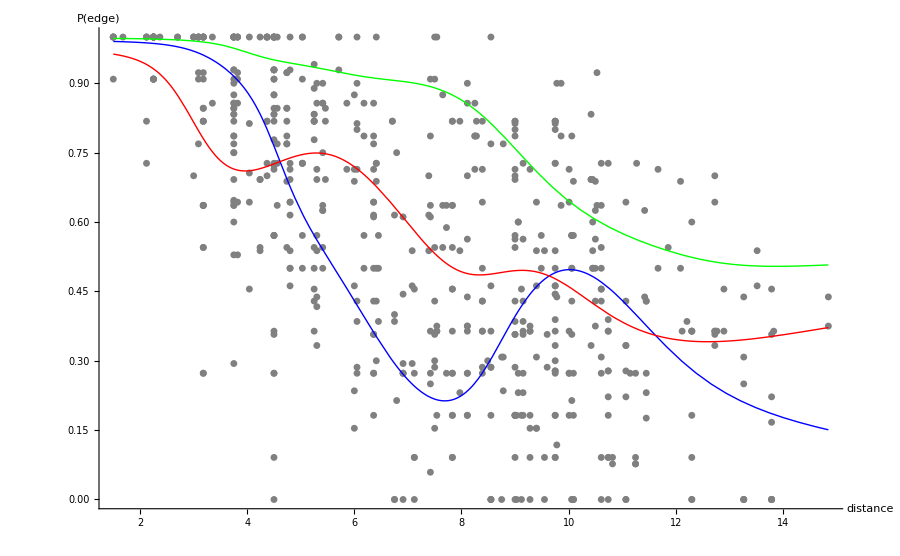

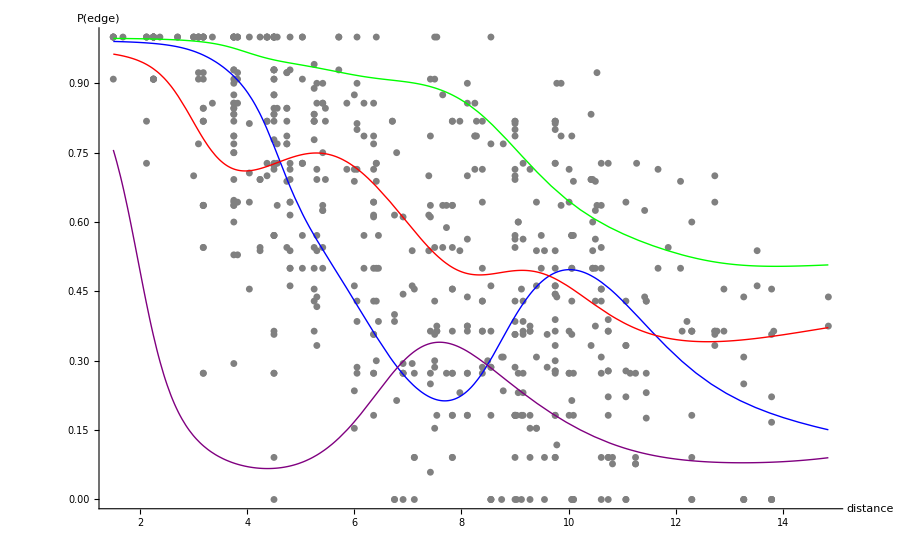

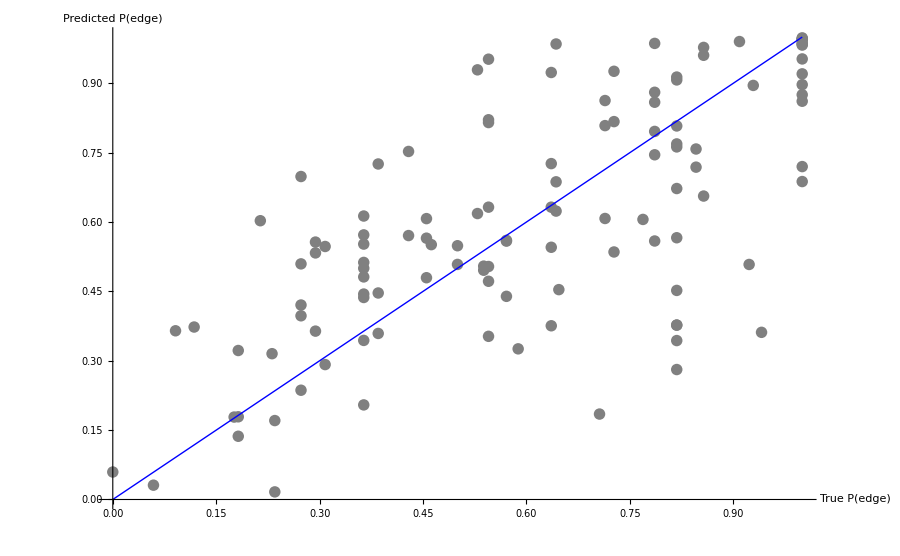

DONE exports:

- trainedNet4_flow_groupSplit.wlnet

- net4_fit_flow_groupSplit.png

- net4_pred_vs_true_test_groupSplit.png

```mathematica
(* ============================================================PhysarumAI—4-input model (FLOW competition+hubs) IMPROVEMENT:GROUP train/test split by ru_ID (no leakage) Features:1) distance(i,j) 2) hubMin=Min(hub(i),hub(j)) 3) hubMax=Max(hub(i),hub(j)) 4) flowCompetition(i,j)=altHubSum/(altHubSum+hub(i)+hub(j)) Target:P_edge from edges_master.csv (0..1) Exports:-trainedNet4_flow_groupSplit.wlnet-net4_fit_flow_groupSplit.png-net4_pred_vs_true_test_groupSplit.png============================================================*)ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];

Print["Current directory: ",Directory[]];
Print["CSV files: ",FileNames["*.csv"]];

(*----------Required files----------*)
If[!FileExistsQ["edges_master.csv"],Print["ERROR: edges_master.csv not found"];Abort[];];
If[!FileExistsQ["adjacency_aggregated.csv"],Print["ERROR: adjacency_aggregated.csv not found"];Abort[];];

SeedRandom[42];
trainFrac=0.8;

(* ============================================================1) Load master edges============================================================*)
master=Import["edges_master.csv","CSV"];
mRows=Rest[master];

(*Expected columns in edges_master:1 ru_ID,2 i,3 j,4 distance,(5 weight),6 P_edge (you used 6 for pEdge)*)
ruList=mRows[[All,1]];
iList=N@mRows[[All,2]];
jList=N@mRows[[All,3]];
dist=N@mRows[[All,4]];
pEdge=N@mRows[[All,6]];

(*Optional:try to detect nTotal in edges_master if it exists*)
headerMaster=master[[1]];
normKey[s_]:=StringReplace[ToLowerCase@StringTrim@ToString[s],{"\""->""," "->"","-"->"","."->"","__"->"_"}];
findCol[header_,possible_List]:=Module[{keys,p},keys=normKey/@header;
p=Flatten@Position[keys,Alternatives@@(normKey/@possible)];
If[p==={},Missing["NotFound"],p[[1]]]];

nTotalColMaster=findCol[headerMaster,{"ntotal","n_total","nrepeats","repeats"}];

nTotalByRuFromMaster=If[nTotalColMaster===Missing["NotFound"],<||>,Module[{pairs},pairs=Table[Module[{ru=ToString[mRows[[k,1]]],nt=Quiet@Check[ToExpression[mRows[[k,nTotalColMaster]]],Missing["NaN"]]},ru=StringTrim@StringReplace[ru,"\""->""];
If[StringLength[ru]>0&&IntegerQ[Round@nt]&&Round@nt>0,ru->Round@nt,Nothing]],{k,1,Length[mRows]}];
Association@pairs]];

(* ============================================================2) Load aggregated adjacency Supports 2 formats:A) ru_ID,i,j,weight B) ru_ID,nTotal,i,j,weight (preferred)============================================================*)
adjAgg=Import["adjacency_aggregated.csv","CSV"];
aHead=adjAgg[[1]];
aRows=Rest[adjAgg];

aHeadN=normKey/@aHead;

(*Detect if adjacency_aggregated contains nTotal as 2nd column by header name*)
nTotalColAdj=findCol[aHead,{"ntotal","n_total","nrepeats","repeats"}];

(*Decide format:if nTotal column exists OR file has>=5 columns and col2 looks like repeats*)
formatHasNTotal=If[nTotalColAdj=!=Missing["NotFound"],True,(*heuristic:if each row has at least 5 cols,and column 2 is numeric and>0 in most rows*)Module[{col2=Quiet@Check[ToExpression/@aRows[[All,2]],{}],ok},ok=If[ListQ[col2]&&Length[col2]>0,Mean[Boole[NumberQ/@col2]]>0.7,False];
ok]];

If[formatHasNTotal,(*----Format B:ru_ID,nTotal,i,j,weight----*)Print["adjacency_aggregated format: ru_ID, nTotal, i, j, weight"];
ruA=aRows[[All,1]];
nTotalA=N@aRows[[All,2]];
iA=N@aRows[[All,3]];
jA=N@aRows[[All,4]];
wA=N@aRows[[All,5]];
nTot[ru_]:=Module[{pos=FirstPosition[ruA,ru,Missing["NoRU"]]},If[pos===Missing["NoRU"],Missing["NoRU"],Round@nTotalA[[pos[[1]]]]]],(*----Format A:ru_ID,i,j,weight----*)Print["adjacency_aggregated format: ru_ID, i, j, weight"];
Print["NOTE: adjacency_aggregated has NO nTotal column. I will try to use nTotal from edges_master.csv."];
ruA=aRows[[All,1]];
iA=N@aRows[[All,2]];
jA=N@aRows[[All,3]];
wA=N@aRows[[All,4]];
If[Length[nTotalByRuFromMaster]==0,Print["ERROR: No nTotal found in adjacency_aggregated AND no nTotal column detected in edges_master.csv."];
Print["Fix: use adjacency_aggregated with columns ru_ID,nTotal,i,j,weight OR add nTotal to edges_master."];
Abort[];];
nTot[ru_]:=Lookup[nTotalByRuFromMaster,ToString[ru],Missing["NoRU"]];];

ruIDs=Union[ruA];

(*Probability per aggregated edge*)
pA=MapThread[Function[{w,ru},Module[{nt=nTot[ru]},If[NumericQ[nt]&&nt>0,N@Clip[w/nt,{0,1}],0.0]]],{wA,ruA}];

(*----------hubs per ru:hub(ru,node)=sum of incident P_edge----------*)
hubByRu=Association@Table[Module[{sub,hubs},sub=Pick[Transpose[{iA,jA,pA}],ruA,ru];(*{i,j,p}*)hubs=Merge[Join[(#[[1]]->#[[3]])&/@sub,(*add p to node i*)(#[[2]]->#[[3]])&/@sub    (*add p to node j*)],Total];
ru->hubs],{ru,ruIDs}];

hubVal[ru_,node_]:=Module[{h=Lookup[hubByRu,ru,<||>]},N@Lookup[h,node,0.0]];

hubI=MapThread[hubVal,{ruList,iList}];
hubJ=MapThread[hubVal,{ruList,jList}];

hubMinAll=MapThread[Min,{hubI,hubJ}];
hubMaxAll=MapThread[Max,{hubI,hubJ}];

(* ============================================================3) Neighbors per ru (weight>0)============================================================*)
neighborsByRu=Association@Table[Module[{sub,rules,nb},sub=Pick[Transpose[{iA,jA,wA}],ruA,ru];(*{i,j,w}*)sub=Select[sub,#[[3]]>0&];
rules=Join[(#[[1]]->#[[2]])&/@sub,(#[[2]]->#[[1]])&/@sub];
nb=Merge[Association/@rules,Union];
ru->nb],{ru,ruIDs}];

neighborList[ru_,node_]:=Module[{nb=Lookup[neighborsByRu,ru,<||>]},Lookup[nb,node,{}]];

(* ============================================================4) flowCompetition============================================================*)
flowCompetition[ru_,i_,j_,hi_,hj_]:=Module[{h,nI,nJ,others,altSum,denom},h=Lookup[hubByRu,ru,<||>];
If[!AssociationQ[h],Return[Missing["NoRU"]]];
nI=neighborList[ru,i];
nJ=neighborList[ru,j];
others=Union@Join[nI,nJ];
others=DeleteCases[others,i|j];
altSum=Total[Lookup[h,others,0.0]];
denom=altSum+hi+hj;
If[NumericQ[denom]&&denom>0,N@Clip[altSum/denom,{0,1}],0.0]];

flowCompAll=MapThread[flowCompetition,{ruList,iList,jList,hubI,hubJ}];

(* ============================================================5) Filter and build dataset============================================================*)
goodMask=MapThread[(NumericQ[#1]&&NumericQ[#2]&&NumericQ[#3]&&NumericQ[#4]&&NumericQ[#5]&&0<=#4<=1&&0<=#5<=1)&,{dist,hubMinAll,hubMaxAll,flowCompAll,pEdge}];

ruGood=Pick[ruList,goodMask,True];

X1=Pick[dist,goodMask,True];
X2=Pick[hubMinAll,goodMask,True];
X3=Pick[hubMaxAll,goodMask,True];
X4=Pick[flowCompAll,goodMask,True];
Y=Pick[pEdge,goodMask,True];

Print["Rows used:         ",Length[Y]];
Print["Unique ru_ID used: ",Length[Union[ruGood]]];

If[Length[Y]<30,Print["ERROR: too few rows after filtering"];
Abort[];];

(* ============================================================6) GROUP train/test split by ru_ID (no leakage)============================================================*)
ruUnique=Union[ruGood];
ruUniqueShuf=RandomSample[ruUnique];

cutRu=Max[1,Round[trainFrac Length[ruUniqueShuf]]];
ruTrainSet=ruUniqueShuf[[;;cutRu]];
ruTestSet=ruUniqueShuf[[cutRu+1;;]];

isTrain=MemberQ[ruTrainSet,#]&/@ruGood;
trainIdx=Flatten@Position[isTrain,True];
testIdx=Flatten@Position[isTrain,False];

Xall=Transpose[{X1,X2,X3,X4}];

Xtrain=Xall[[trainIdx]];
Ytrain=Y[[trainIdx]];

Xtest=Xall[[testIdx]];
Ytest=Y[[testIdx]];

Print["Train ru_ID: ",Length[ruTrainSet],"   Test ru_ID: ",Length[ruTestSet]];
Print["Train rows:  ",Length[trainIdx],"   Test rows:  ",Length[testIdx]];

If[Length[testIdx]<10,Print["ERROR: too few test rows"];
Abort[];];

(* ============================================================7) Standardize features using TRAIN only============================================================*)
mu=Mean/@Transpose[Xtrain];
sig=StandardDeviation/@Transpose[Xtrain];
sig=Map[If[#==0,1.0,#]&,sig];

z[x_List]:=(x-mu)/sig;

XtrainZ=z/@Xtrain;
XtestZ=z/@Xtest;

trainData=Thread[XtrainZ->(List/@Ytrain)];
testData=Thread[XtestZ->(List/@Ytest)];

(* ============================================================8) Define+train net============================================================*)
net4=NetChain[{LinearLayer[32],Tanh,LinearLayer[16],Tanh,LinearLayer[1],LogisticSigmoid},"Input"->4];

trainedNet4=Check[NetTrain[net4,trainData,MaxTrainingRounds->1800,BatchSize->256,Method->"ADAM"],$Failed];

If[trainedNet4===$Failed,Print["ERROR: NetTrain failed"];
Abort[];];

(* ============================================================9) Metrics on TEST============================================================*)
predTest=trainedNet4/@(First/@testData);
pred1=predTest[[All,1]];
true1=(Last/@testData)[[All,1]];

mae=Mean[Abs[pred1-true1]];
rmse=Sqrt[Mean[(pred1-true1)^2]];
corr=If[Length[pred1]>2,Correlation[pred1,true1],Indeterminate];

Print["TEST MAE  = ",mae];
Print["TEST RMSE = ",rmse];
Print["TEST Corr = ",corr];

(* ============================================================10) Plot A:scatter+3 curves (fix flowComp at median)============================================================*)
dMin=N@Min[X1];
dMax=N@Max[X1];

hubMinLow=N@Quantile[X2,0.2];
hubMinMed=N@Median[X2];
hubMinHigh=N@Quantile[X2,0.8];

hubMaxLow=N@Quantile[X3,0.2];
hubMaxMed=N@Median[X3];
hubMaxHigh=N@Quantile[X3,0.8];

fcMed=N@Median[X4];

scatterAll=ListPlot[Transpose[{X1,Y}],PlotStyle->Gray,PlotRange->{0,1},AxesLabel->{"distance","P(edge)"},ImageSize->900];

curveLow=Plot[trainedNet4[z[{d,hubMinLow,hubMaxLow,fcMed}]][[1]],{d,dMin,dMax},PlotStyle->{Blue,Thick}];

curveMed=Plot[trainedNet4[z[{d,hubMinMed,hubMaxMed,fcMed}]][[1]],{d,dMin,dMax},PlotStyle->{Red,Thick}];

curveHigh=Plot[trainedNet4[z[{d,hubMinHigh,hubMaxHigh,fcMed}]][[1]],{d,dMin,dMax},PlotStyle->{Green,Thick}];

fitPlot4=Show[{scatterAll,curveLow,curveMed,curveHigh},PlotRange->{0,1},ImageSize->900,AxesLabel->{"distance","P(edge)"},PlotLegends->Placed[{"low hubs","median hubs","high hubs"},Above]];

fitPlot4
(*---4th curve:one low hub,one high hub (asymmetric case)---*)curveLowHigh=Plot[trainedNet4[z[{d,hubMinLow,hubMaxHigh,fcMed}]][[1]],{d,dMin,dMax},PlotStyle->{Purple,Thick}];

fitPlot4=Show[{scatterAll,curveLow,curveMed,curveHigh,curveLowHigh},PlotRange->{0,1},ImageSize->900,AxesLabel->{"distance","P(edge)"},PlotLegends->Placed[{"low–low hubs","med–med hubs","high–high hubs","low–high hubs"},Above]];

fitPlot4

(* ============================================================11) Plot B:Pred vs True on TEST+diagonal============================================================*)
predVsTrue=ListPlot[Transpose[{true1,pred1}],PlotStyle->Gray,PlotRange->{{0,1},{0,1}},AxesLabel->{"True P(edge)","Predicted P(edge)"},ImageSize->900];

diag=Plot[x,{x,0,1},PlotStyle->{Blue,Thick}];

predVsTruePlot=Show[{predVsTrue,diag},ImageSize->900];
predVsTruePlot

(* ============================================================12) Export============================================================*)
Export["trainedNet4_flow_groupSplit.wlnet",trainedNet4];
Export["net4_fit_flow_groupSplit.png",fitPlot4];
Export["net4_pred_vs_true_test_groupSplit.png",predVsTruePlot];

Print["DONE exports:"];
Print["- trainedNet4_flow_groupSplit.wlnet"];
Print["- net4_fit_flow_groupSplit.png"];
Print["- net4_pred_vs_true_test_groupSplit.png"];
```

```mathematica
(* ============================================================EXTRA PLOT:hubMin vs hubMax (distance fixed,flowComp fixed)============================================================*)dFixed=N@Median[X1];   (*фиксируем расстояние*)
fcFixed=N@Median[X4];   (*фиксируем flowCompetition*)

(*диапазоны хабов возьмём по квантилям,чтобы не улетать в редкие хвосты*)
hMinRange={N@Quantile[X2,0.05],N@Quantile[X2,0.95]};
hMaxRange={N@Quantile[X3,0.05],N@Quantile[X3,0.95]};

(*важный момент:hubMin должен быть<=hubMax.Поэтому делаем теплокарту по (hMin,hMax),но зануляем область где hMin>hMax.*)

hubMinHubMaxHeat=DensityPlot[If[hmin<=hmax,trainedNet4[z[{dFixed,hmin,hmax,fcFixed}]][[1]],Indeterminate],{hmin,hMinRange[[1]],hMinRange[[2]]},{hmax,hMaxRange[[1]],hMaxRange[[2]]},PlotRange->{0,1},Frame->True,FrameLabel->{"hubMin","hubMax"},PlotLabel->Row[{"Predicted P(edge) vs hubMin & hubMax (distance fixed at ",NumberForm[dFixed,{4,2}],", flowComp fixed at ",NumberForm[fcFixed,{4,2}],")"}],PlotPoints->45,MaxRecursion->2,ImageSize->900];

hubMinHubMaxHeat
```

-Graphics-

```mathematica
hubMinHubMax3D=Plot3D[If[hmin<=hmax,trainedNet4[z[{dFixed,hmin,hmax,fcFixed}]][[1]],Indeterminate],{hmin,hMinRange[[1]],hMinRange[[2]]},{hmax,hMaxRange[[1]],hMaxRange[[2]]},PlotRange->{0,1},AxesLabel->{"hubMin","hubMax","P(edge)"},PlotLabel->"3D: P(edge) as function of hubMin & hubMax (distance & flowComp fixed)",PlotPoints->40,MaxRecursion->2,ImageSize->900];

hubMinHubMax3D
```